## Funktionsgraphen und Vektoren

Funktionen haben einen Graph, den man plotten kann.

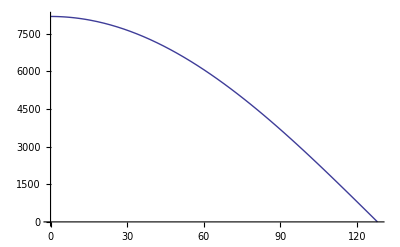

```mathematica
Clear["Global`*"]
a=2^13;
z=128;
f[x_]:=a*Cos[(Pi/2)*x/z];
Plot[f[x],{x,0,z}]
```

Man kann Funktionen einen Vektor zuordenen, indem man sich den Vektor an bestimmten stellen anschaut, etwa an fünf oder sechs (oder zehn) Punkten

{8192.,8179.99,8143.98,8084.08,8000.48,7893.4,7763.17,7610.18,7434.86,7237.73,7019.37,6780.43,6521.59,6243.63,5947.36,5633.63,5303.39,4957.59,4597.24,4223.42,3837.2,3439.73,3032.17,2615.72,2191.59,1761.04,1325.32,885.711,443.506,5.01615×10^-13}

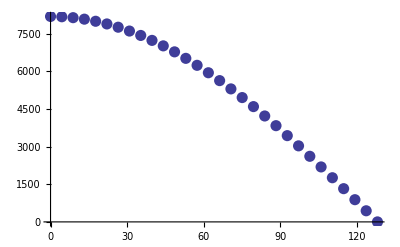

```mathematica
n = 30;
b=Table[f[x],{x,0.0,z,z/(n-1)}]
dots=ListPlot[Table[{x,f[x]},{x,0.0,z,z/(n-1)}],PlotStyle->{AbsolutePointSize[8]}]
```

Wir besorgen uns jetzt noch m andere Funktionen, nämlich Polynome.

```mathematica
m=3;
poly={1,x^2, x^4};
```

```mathematica
m=2
poly={1,x^2}
```

2

{1,x^2}

und für jedes Polynom einen Vektor (schon wieder). Diesmal sehen aber die Vektoren ganz anders aus, sie bestehen nämlich aus den Werten, die die Polynome im Intervall 0 bis z an sechs Stellen haben.

```mathematica
A = Table[Table[poly[[i]],{i,1,m}],{x,0.0,z,z/(n-1)}];
A//MatrixForm
```

(1 | 0.
1 | 19.4816
1 | 77.9263
1 | 175.334
1 | 311.705
1 | 487.039
1 | 701.337
1 | 954.597
1 | 1246.82
1 | 1578.01
1 | 1948.16
1 | 2357.27
1 | 2805.35
1 | 3292.39
1 | 3818.39
1 | 4383.35
1 | 4987.28
1 | 5630.17
1 | 6312.03
1 | 7032.85
1 | 7792.63
1 | 8591.37
1 | 9429.08
1 | 10305.8
1 | 11221.4
1 | 12176.
1 | 13169.5
1 | 14202.1
1 | 15273.6
1 | 16384.)

Wir können nun versuchen den Graph von Cosinus, genauer den daraus gewonnenen Vektor t als linearkombination der polynomvektoren darzustellen:

```mathematica
xdach = LinearSolve[Transpose[A].A,Transpose[A].b]
```

{8025.37,-0.512775}

Die Linerakombination der Polynom-Vektoren ist gleich dem Vektor t der Cosinusfunktion.

```mathematica
p = A.xdach
b
e=b-p
```

{8025.37,8015.38,7985.41,7935.46,7865.53,7775.63,7665.74,7535.88,7386.03,7216.21,7026.4,6816.62,6586.86,6337.12,6067.4,5777.69,5468.02,5138.36,4788.72,4419.1,4029.5,3619.93,3190.37,2740.84,2271.32,1781.83,1272.36,742.905,193.474,-375.937}

{8192.,8179.99,8143.98,8084.08,8000.48,7893.4,7763.17,7610.18,7434.86,7237.73,7019.37,6780.43,6521.59,6243.63,5947.36,5633.63,5303.39,4957.59,4597.24,4223.42,3837.2,3439.73,3032.17,2615.72,2191.59,1761.04,1325.32,885.711,443.506,5.01615×10^-13}

{166.631,164.607,158.568,148.621,134.941,117.774,97.4337,74.3018,48.8273,21.5244,-7.02869,-36.1915,-65.2631,-93.4844,-120.04,-144.061,-164.627,-180.769,-191.474,-195.684,-192.302,-180.196,-158.201,-125.12,-79.7314,-20.7922,52.9608,142.806,250.032,375.937}

Die linearkombination der Polynome ist (fast) gleich dem Cosinus

```mathematica
lp = poly.xdach
InputForm[xdach]
```

8025.37-0.512775 x^2

{8025.368883441758, -0.5127750130248133}

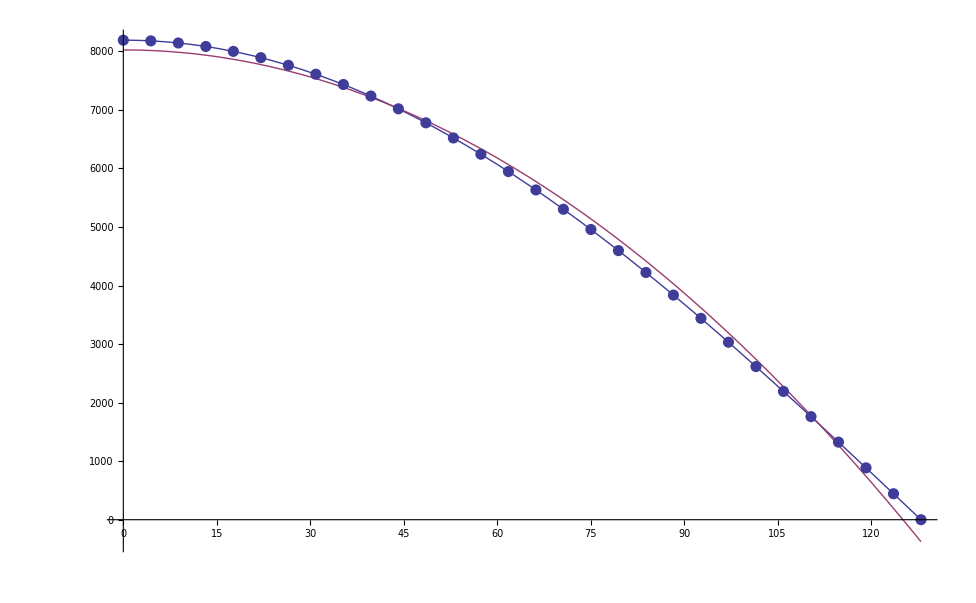

```mathematica
fp=Plot[{f[x],lp},{x,0,z}];
Show[fp,dots]
```

## Zusammenfassung

```mathematica
costab=Table[Round[lp],{x,0,z}];
fcos[i_]:=Module[{t=Mod[i,(4*z)], tt=0}, tt=If[ t>=2*z,4*z-t,t]; If[tt>= z,-costab[[2*z-tt+1]],costab[[tt+1]]]];
freq = 22050;
ton = 440;
schwingungen=freq/ton;
step=Round[4*z/schwingungen];
longtab=Table[fcos[i*step],{i,0,freq*4}];
```

```mathematica
ListPlay[longtab,SampleRate->22050]
```

-Graphics-